### XXX

```mathematica
SetDirectory[NotebookDirectory[]];
paths={"07-63.6mA-33.7C.tab","08-63.6mA-33.6C.tab","09-63.6mA-33.3C.tab","10-63.6mA-33.1C.tab","11-63.6mA-32.8C.tab","12-63.6mA-32.6C.tab"};
Manipulate[
path = paths[[n]];
ch1zoom = 1;
ch2zoom = 1;

data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{""<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], "Spannung der Photodiode"], "Spannung an Spule 5"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"Zeit t/s", "Spannung U / V"}],{n,1,6,1}]
```

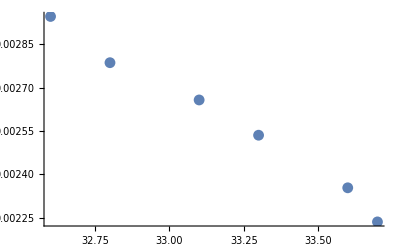

```mathematica
maxpos={{{0.002235,0.2207}},{{0.002353,0.3838}},{{0.002535,0.4487}},{{0.002657,0.623}},{{0.002786,0.6817}},{{0.002946,0.8973}}}[[All,1,1]];
temps={33.7,33.6,33.3,33.1,32.8,32.6};
data=Transpose[{temps,maxpos}];
ListPlot[data]
```